# Plots for the Running of the Mixing Parameters and Masses

This notebook can be used to create plots of the RG evolution, after the RGEs have been solved (RGESolve) in a different notebook.

```mathematica
(* Some preliminary graphics definitions *)
Needs["REAP`RGEPlotUtilities`"];
```

```mathematica
If[$VersionNumber<6,
Get["Graphics`FilledPlot`"];
Get["Graphics`Colors`"],
ForestGreen=RGBColor[0.1,0.75,0.2];
];
```

```mathematica
(* Define the plot region *)
ClearAll[tmin,tmax]
tmin=Log[10,100];
tmax=Log[10,2*10^16];

(* Define the functions that should be plotted *)
ClearAll[Mnu,Ye]
Mnu[mu_]:=RGEGetSolution[mu,RGEMν]//Chop
Ye[mu_]:=RGEGetSolution[mu,RGEYe]//Chop

ClearAll[MixingPars,MixingParsLogScale,NuMasses,NuMassesLogScale]
MixingPars[mu_]:=MNSParameters[Mnu[mu],Ye[mu]]⟦1⟧
MixingParsLogScale[x_]:=MixingPars[10^x]
NuMasses[mu_]:=MNSParameters[Mnu[mu],Ye[mu]]⟦2⟧
NuMassesLogScale[x_]:=NuMasses[10^x]

ClearAll[θ12,θ13,θ23,δ,φ1,φ2,m1,m2,m3,Δm2sol,Δm2atm]
θ12[t_]:=MixingParsLogScale[t]⟦1⟧/Degree
θ13[t_]:=MixingParsLogScale[t]⟦2⟧/Degree
θ23[t_]:=MixingParsLogScale[t]⟦3⟧/Degree
δ[t_]:=MixingParsLogScale[t]⟦4⟧/Degree
φ1[t_]:=MixingParsLogScale[t]⟦8⟧/Degree
φ2[t_]:=MixingParsLogScale[t]⟦9⟧/Degree
m1[t_]:=NuMassesLogScale[t]⟦1⟧
m2[t_]:=NuMassesLogScale[t]⟦2⟧
m3[t_]:=NuMassesLogScale[t]⟦3⟧
Δm2sol[t_]:=m2[t]^2-m1[t]^2
Δm2atm[t_]:=m3[t]^2-m2[t]^2

(* Positions of the thresholds *)
ClearAll[M1,M2,M3,ShadowEFT]
{M1,M2,M3}=RGEGetTransitions[]⟦{4,3,2},1⟧;
ShadowEFT=RGEShadowEFT[M1,M2,M3,10^17];
```

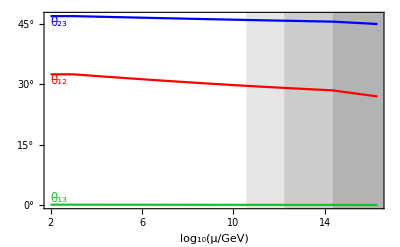

```mathematica
(* Draw the plot for the mixing angles *)
Show[Plot[
{θ12[t],θ13[t],θ23[t]},{t,tmin,tmax},
ImageSize->400,FrameLabel->{"log_10(μ/GeV)",""},FrameTicks->{RGELogTicksLabeled[2,19],Table[{i*15,ToString[i*15]<>"°"},{i,0,3}],RGELogTicks[2,19],Table[{i*15,""},{i,0,3}]},
PlotRange->{All,All},PlotStyle->{Red,ForestGreen,Blue},
Prolog->{ShadowEFT},
Epilog->{
Text[StyleForm[Subscript[θ, 12],FontColor->Red,FontSize->12],{tmin,θ12[tmin]},{-0.8,1.4}],
Text[StyleForm[Subscript[θ, 13],FontColor->ForestGreen,FontSize->12],{tmin,θ13[tmin]},{-0.8,-1}],
Text[StyleForm[Subscript[θ, 23],FontColor->Blue,FontSize->12],{tmin,θ23[tmin]},{-0.8,1.4}]},
DisplayFunction->Identity
],DisplayFunction->$DisplayFunction]
```

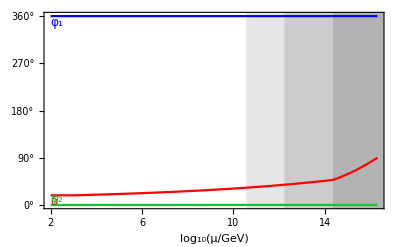

```mathematica
(* Draw the plot for the phases *)
Show[Plot[
{δ[t],φ1[t],φ2[t]},{t,tmin,tmax},
ImageSize->400,FrameLabel->{"log_10(μ/GeV)",""},FrameTicks->{RGELogTicksLabeled[2,19],Table[{i*45,ToString[i*45]<>"°"},{i,0,8}],RGELogTicks[2,19],Table[{i*45,""},{i,0,12}]},
PlotRange->{All,All},PlotStyle->{Red,Blue,ForestGreen},
Prolog->{ShadowEFT},
Epilog->{
Text[StyleForm[δ,FontColor->Red,FontSize->12],{tmin,δ[tmin]},{-0.8,1.4}],
Text[StyleForm[Subscript[φ, 1],FontColor->Blue,FontSize->12],{tmin,φ1[tmin]},{-0.8,1.4}],
Text[StyleForm[Subscript[φ, 2],FontColor->ForestGreen,FontSize->12],{tmin,φ2[tmin]},{-0.8,-1}]},
DisplayFunction->Identity
],DisplayFunction->$DisplayFunction]
```

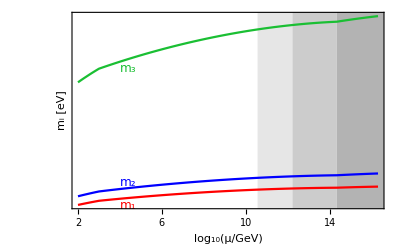

```mathematica
(* Draw the plot for the mass eigenvalues *)
tlabel=4;   (* Position where the labels m1,m2,m3 should be placed *)
Show[Plot[
{m1[t],m2[t],m3[t]},{t,tmin,tmax},
ImageSize->400,FrameLabel->{"log_10(μ/GeV)","m_i [eV]"},FrameTicks->{RGELogTicksLabeled[2,19],Table[{i*0.01,PaddedForm[i*0.01,{3,2}]},{i,0,50}],RGELogTicks[2,19],Table[{i*0.01,""},{i,0,50}]},
PlotRange->{All,All},PlotStyle->{Red,Blue,ForestGreen},
Prolog->{ShadowEFT},
Epilog->{
Text[StyleForm[Subscript[m, 1],FontColor->Red,FontSize->12],{tlabel,m1[tlabel]},{-0.8,1.4}],
Text[StyleForm[Subscript[m, 2],FontColor->Blue,FontSize->12],{tlabel,m2[tlabel]},{-0.8,-2}],
Text[StyleForm[Subscript[m, 3],FontColor->ForestGreen,FontSize->12],{tlabel,m3[tlabel]},{-0.8,1.4}]},
DisplayFunction->Identity
],DisplayFunction->$DisplayFunction]
```

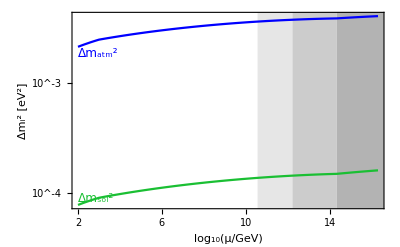

```mathematica
(* Draw the plot for the mass squared differences (on a logarithmic scale) *)
Show[Plot[
{Log[10,Abs[Δm2sol[t]]],Log[10,Abs[Δm2atm[t]]]},{t,tmin,tmax},
ImageSize->400,FrameLabel->{"log_10(μ/GeV)","Δm_i^2 [eV^2]"},FrameTicks->{RGELogTicksLabeled[2,19],RGELogTicksLabeledNegExp[-6,-1],RGELogTicks[2,19],RGELogTicks[-6,-1]},
PlotRange->{All,All},PlotStyle->{ForestGreen,Blue},
Prolog->{ShadowEFT},
Epilog->{
Text[StyleForm[Subscript[Δm, sol]^2,FontColor->ForestGreen,FontSize->12],{tmin,Log[10,Abs[Δm2sol[tmin]]]},{-0.8,-2}],
Text[StyleForm[Subscript[Δm, atm]^2,FontColor->Blue,FontSize->12],{tmin,Log[10,Abs[Δm2atm[tmin]]]},{-0.8,1.4}]},
DisplayFunction->Identity
],DisplayFunction->$DisplayFunction]
```

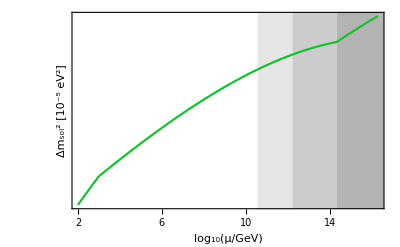

```mathematica
(* Draw the plot for the solar mass squared difference (on a linear scale) *)
Show[Plot[
Δm2sol[t]*10^5,{t,tmin,tmax},
ImageSize->400,FrameLabel->{"log_10(μ/GeV)","Δm_sol^2 [10^-5 eV^2]"},FrameTicks->{RGELogTicksLabeled[2,19],Table[{i,i},{i,-100,100}],RGELogTicks[2,19],Table[{i,""},{i,-100,100}]},
PlotRange->{All,All},PlotStyle->{ForestGreen},
Prolog->{ShadowEFT},
DisplayFunction->Identity
],DisplayFunction->$DisplayFunction]
```

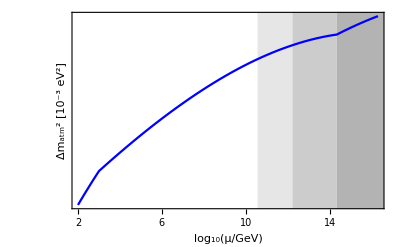

```mathematica
(* Draw the plot for the atmospheric mass squared difference (on a linear scale) *)
Show[Plot[
Δm2atm[t]*10^3,{t,tmin,tmax},
ImageSize->400,FrameLabel->{"log_10(μ/GeV)","Δm_atm^2 [10^-3 eV^2]"},FrameTicks->{RGELogTicksLabeled[2,19],Table[{i*0.2,PaddedForm[i*0.2,{2,1}]},{i,-50,50}],RGELogTicks[2,19],Table[{i*0.2,""},{i,0,50}]},
PlotRange->{All,All},PlotStyle->{Blue},
Prolog->{ShadowEFT},
DisplayFunction->Identity
],DisplayFunction->$DisplayFunction]
```